```mathematica
sol = u/.NDSolve[{D[u[t,x], t] == 0.5 D[u[t,x],x,x]+u[t,x]D[u[t,x],x],  u[t,-Pi] == u[t, Pi] == 0 , u[0,x] == Sin[x]}, u, {t,0,2},{x,-Pi, Pi}][[1]]
```

InterpolatingFunction[{{0.,2.},{-3.14159,3.14159}},<>]

0.5 InterpolatingFunction[{{0.,2.},{-3.14159,3.14159}},<>][t,x]

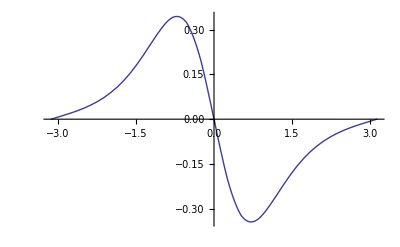

```mathematica
Eq1=0.5 D[u[t,x],x,x];
Magnitude1[t_,x_]=Eq1/.u->sol
Plot[Magnitude1[1.5,x],{x,-π,π}]
```

InterpolatingFunction[{{0.,2.},{-3.14159,3.14159}},<>][t,x] InterpolatingFunction[{{0.,2.},{-3.14159,3.14159}},<>][t,x]

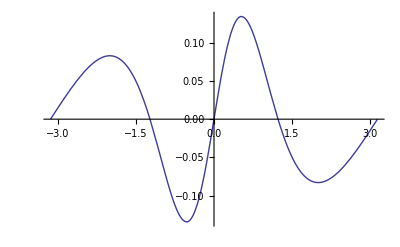

```mathematica
Eq2=u[t,x]D[u[t,x],x];
Magnitude2[t_,x_]=Eq2/.u->sol
Plot[Magnitude2[1.5,x],{x,-π,π}]
```